```mathematica
Clear["Global`*"]

βOLS={0.6,0.75};

kmax=2.5;
kmin=0;
dk=-0.005;

λmax=0;
λmin=0.5;
dλ=0.005;

b1min=0;
b1max=0.8;
db1=0.01;
b2min=0;
b2max=0.8;
db2=0.01;

S[b_]:=-b.βOLS+1/2b.b;
normq[x_,y_,q_]:=(Abs[x]^q+Abs[y]^q)^(1/q)
SLagr[b_,λ_,q_]:=-b.βOLS+1/2b.b+λ normq[b[[1]],b[[2]],q]^q

b1=Table[i,{i,b1min,b1max,db1}];
b2=Table[i,{i,b2min,b2max,db2}];

L=Table[0,{Length[b1]},{Length[b2]}];
For[i=1,i≤Length[b1],i++,
For[l=1,l≤Length[b2],l++,
L[[i,l]]=S[{b1[[i]],b2[[l]]}]
]
];

q=0.5;

ks=Table[i,{i,kmax,kmin,dk}];
λs=Table[i,{i,λmax,λmin,dλ}];
x=Table[0,Length[ks]];
y=Table[0,Length[ks]];
xLagr=Table[0,Length[λs]];
yLagr=Table[0,Length[λs]];

For[j = 1,j≤Length[ks],j++,
If[Mod[j,50]==0,Print["k index = "<>ToString[j]],""];

z=Outer[(Abs[#1]^q+Abs[#2]^q)^(1/q) &,b1,b2];
pos=Position[z,_?(#≤ks[[j]]&)];

Ltest=Table[0,Length[pos]];

For[i=1,i≤Length[Ltest],i++,
pos1=pos[[i]][[1]]//Quiet;
pos2=pos[[i]][[2]]//Quiet;
Ltest[[i]]=L[[pos1,pos2]]//Quiet;
];

minpos=Position[Ltest,Min[Ltest]]//Flatten;
minposx=(pos[[minpos]]//Flatten)[[1]]//Quiet;
minposy=(pos[[minpos]]//Flatten)[[2]]//Quiet;
x[[j]]=b1[[minposx]]//Quiet;
y[[j]]=b2[[minposy]]//Quiet;

]

For[j=1,j≤Length[λs],j++,

If[Mod[j,50]==0,Print["λ index = "<>ToString[j]],""];
LtestLagr=Table[0,{Length[b1]},{Length[b2]}];

For[i=1,i≤Length[b1],i++,
For[l=1,l≤Length[b2],l++,
LtestLagr[[i,l]]=SLagr[{b1[[i]],b2[[l]]},λs[[j]],q]
]
];

minposLagr=Position[LtestLagr,Min[LtestLagr]]//Flatten;
xLagr[[j]]=b1[[minposLagr[[1]]]];
yLagr[[j]]=b2[[minposLagr[[2]]]];
]
```

k index = 50

k index = 100

k index = 150

k index = 200

k index = 250

k index = 300

k index = 350

k index = 400

k index = 450

k index = 500

λ index = 50

λ index = 100

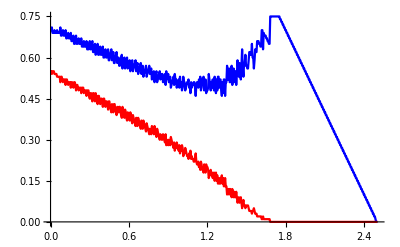

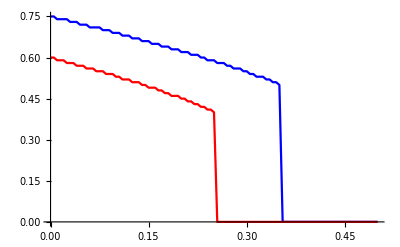

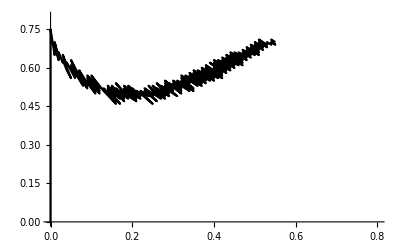

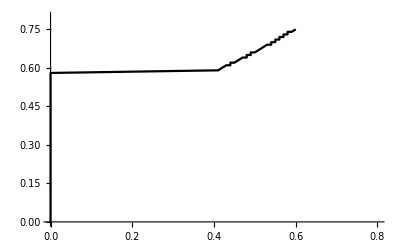

```mathematica
px=ListLinePlot[{Transpose[{ks,Reverse[x]}]},PlotStyle->Red];
py=ListLinePlot[{Transpose[{ks,Reverse[y]}]},PlotStyle->Blue];
Show[py,px]

pxLagr=ListLinePlot[{Transpose[{λs,xLagr}]},PlotStyle->Red];
pyLagr=ListLinePlot[{Transpose[{λs,yLagr}]},PlotStyle->Blue];
Show[pyLagr,pxLagr]

ListLinePlot[Transpose[{x,y}],PlotRange->{{b1min,b1max},{b2min,b2max}},PlotStyle->Black]
ListLinePlot[Transpose[{xLagr,yLagr}],PlotRange->{{b1min,b1max},{b2min,b2max}},PlotStyle->Black]
```

```mathematica
Clear["Global`*"]
Minimize[{-x*b+1/2x^2,Abs[x]^(1/2)≤t,t>0},x]
```

{Piecewise[{{-b^2/2, t>0&&-t^2<b≤t^2}, {1/2 (-2 b t^2+t^4), t>0&&b>t^2}, {1/2 (2 b t^2+t^4), (t>0&&b==-t^2)||(t>0&&b<-t^2)}, {∞, True}}],{x→Piecewise[{{b, t>0&&-t^2<b≤t^2}, {b-√((b-t^2)^2), t>0&&b>t^2}, {b-√((b+t^2)^2), t>0&&b==-t^2}, {b+√((b+t^2)^2), t>0&&b<-t^2}, {Indeterminate, True}}]}}